```mathematica
(* Graphics Primitives *)
RatHead = Graphics[{
Line[{{0,3},{-1.75, 0}}],
Line[{{0,3},{1.75,0}}],
Line[{{-1.75,0},{-1.75,-0.4}}],
Line[{{1.75,0},{1.75, -0.4}}],
BezierCurve[{{-1.75,-0.4},{0, -3},{1.75, -0.4}}],
BezierCurve[{{-1.75,0},{-2.5, -0.35},{-2, -0.6},{-1.75, -0.4}}],
BezierCurve[{{1.75,0},{2.5, -0.35},{2, -0.6},{1.75, -0.4}}]
}];

RestCL = Graphics[{ Black,Dashed,Line[{{0,-4},{0,4}}]}];

RatNeck= Graphics[{Line[{{-0.75, -1.45},{-1, -3}}], Line[{{0.75, -1.45},{1, -3}}]}];

LeftWhiskers = Graphics[{Line[{{-0.27, 2.5},{-2.5, 4}}],Line[{{-1.25, 0.85},{-4.4, 3}}]}];

RightWhiskers = Graphics[{Line[{{0.27, 2.5},{2.5, 4}}],Line[{{1.25, 0.85},{4.4, 3}}]}];

RestState = Show[RatHead, RestCL,RatNeck, RightWhiskers, LeftWhiskers];

SimList= {RestState};

HeadAngles = {0};
list = {};
For[i=-1.047,i<1.047, i=i+Pi/360,
HeadAngles =Append[HeadAngles, Sin[i]];
];
Length[HeadAngles]
j=0;

(* Head and Whisker Movement *)
While[j<Length[HeadAngles],
(*While[j< Length[RightWhiskersAngles] && k< Length[LeftWhiskersAngles],*)

(* Head Movement *)
headTurn = Graphics[Rotate[RatHead,HeadAngles[[j]]]];

(* Right Whisker Movement *)
(*rightWhiskerTurn = Rotate[RightWhiskers, RightWhiskers[[j]]];

(* Left Whisker Movement *)
leftWhiskerTurn = Rotate[LeftWhiskers, LeftWhiskers[[k]]];
];*)
nextPose= Show[headTurn,RestCL,RatNeck, RightWhiskers, LeftWhiskers];
SimList = Append[SimList, nextPose];
j++;
];

(* Animation *)
ListAnimate[SimList,AnimationRunning->False, AnimationRate->Automatic]
```

241

Show::gcomb: Could not combine the graphics objects in TraditionalForm`.

General::stop: Further output of Show :: gcomb will be suppressed during this calculation.

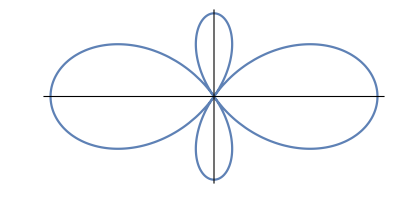

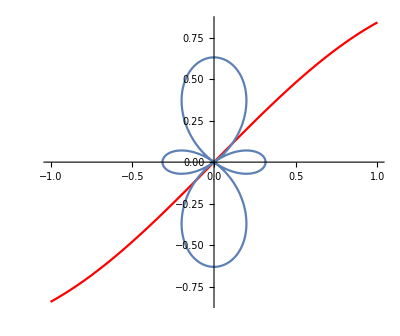

```mathematica
Y20=PolarPlot[Abs[Sqrt[5/(16*Pi)]*(3*Cos[Theta]^2-1)],{Theta,0,2*Pi},Ticks->None]
Show[{Plot[Sin[x],{x,-1,1},PlotStyle->Red],Graphics[Rotate[Y20[[1]],Pi/2,{0,0}]]},PlotRange->1,AspectRatio->Automatic,BaseStyle->{18,Bold,Thick}]
```